```mathematica
Clear[x,y,t]
sys={x''[t]==-10x[t]+4y[t],y''[t]==-4y[t]+4x[t]}
```

{x''[t]==-10 x[t]+4 y[t],y''[t]==4 x[t]-4 y[t]}

```mathematica
paso1=LaplaceTransform[sys,t,s]
```

{s^2 LaplaceTransform[x[t],t,s]-s x[0]-x'[0]==-10 LaplaceTransform[x[t],t,s]+4 LaplaceTransform[y[t],t,s],s^2 LaplaceTransform[y[t],t,s]-s y[0]-y'[0]==4 LaplaceTransform[x[t],t,s]-4 LaplaceTransform[y[t],t,s]}

```mathematica
paso2=paso1/.{x[0]->0,x'[0]->1,y[0]->0,y'[0]->-1}
```

{-1+s^2 LaplaceTransform[x[t],t,s]==-10 LaplaceTransform[x[t],t,s]+4 LaplaceTransform[y[t],t,s],1+s^2 LaplaceTransform[y[t],t,s]==4 LaplaceTransform[x[t],t,s]-4 LaplaceTransform[y[t],t,s]}

```mathematica
paso3=Solve[paso2,{LaplaceTransform[x[t],t,s],LaplaceTransform[y[t],t,s]}]//Simplify
```

{{LaplaceTransform[x[t],t,s]→s^2/(24+14 s^2+s^4),LaplaceTransform[y[t],t,s]→-(6+s^2)/(24+14 s^2+s^4)}}

```mathematica
x[t_]=InverseLaplaceTransform[paso3[[1,1,2]],s,t]
```

-Sin[√2 t]/(5 √2)+1/5 √3 Sin[2 √3 t]

```mathematica
y[t_]=InverseLaplaceTransform[paso3[[1,2,2]],s,t]
```

1/10 (-2 √2 Sin[√2 t]-√3 Sin[2 √3 t])

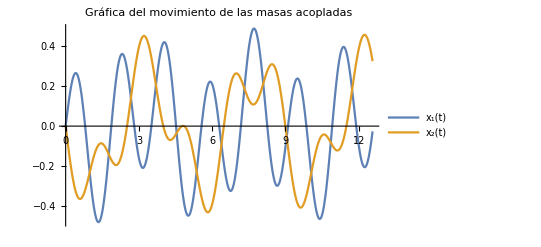

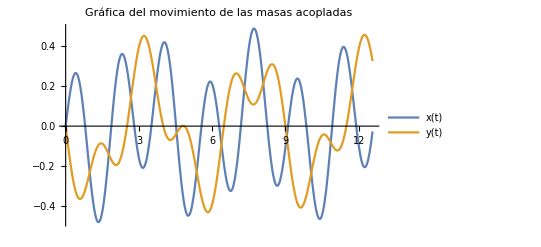

```mathematica
Plot[{x[t],y[t]},{t,0,4Pi}, PlotLegends->{"x_1(t)", "x_2(t)"}, PlotLabel->"Gráfica del movimiento de las masas acopladas", LabelStyle->Directive[FontSize->12]]
Plot[{x[t],y[t]},{t,0,4Pi}, PlotLegends->"Expressions", PlotLabel->"Gráfica del movimiento de las masas acopladas", LabelStyle->Directive[FontSize->12]]
```

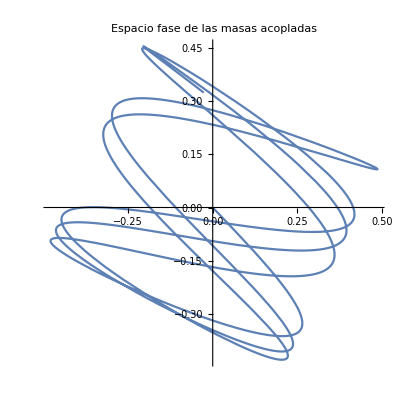

```mathematica
ParametricPlot[{x[t],y[t]},{t,0,4Pi},AspectRatio->1, PlotLabel->"Espacio fase de las masas acopladas",LabelStyle->Directive[FontSize->12]]
```

```mathematica
Clear[spring,zigzag,length,points,pairs]
zigzag[{a_,b_},{c_,d_},n_,eps_]:=
Module[{length,points,pairs},
length = d-b;
points =Table[b+i length/n,{i,1,n-1}];
pairs=Table[{a+(-1)^i eps,points[[i]]},{i,1,n-1}];
PrependTo[pairs,{a,b}];
AppendTo[pairs,{c,d}];
Line[pairs]
]
```

```mathematica
spring2[t_,len1_,len2_,opts___]:=
Show[Graphics[
{zigzag[{0,-x[t]},{0,len1},20,0.025],
PointSize[0.025],Point[{0,len1}],
zigzag[{0,-y[t]-len2},{0,-x[t]},20,0.025],
PointSize[0.075],Point[{0,.05-x[t]}],
PointSize[0.05],Point[{0,-y[t]-len2}]}],opts,
Axes->Automatic,
AxesStyle->GrayLevel[0.5],
Ticks-> None,
AspectRatio-> 1,
PlotRange-> {{-1/2,1/2},{-2.2,1.2}},
DisplayFunction-> Identity]
```

```mathematica
tvals=Table[t,{t,0,4 Pi, 4 Pi/15}];
```

```mathematica
graphs=Map[spring2[#,1,1]&,tvals];
toshow=Partition[graphs,4];
Show[GraphicsGrid[toshow]]
```

-Graphics-

```mathematica
Do[spring2[t,1,1,DisplayFunction-> $DisplayFunction],{t,0,4,4/31}]
```